```mathematica
a= 0.1
```

0.1

```mathematica
x = Table[i,{i, 0, 40}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
L = Table[Cos[a*p], {p, x}]
```

{1.,0.995004,0.980067,0.955336,0.921061,0.877583,0.825336,0.764842,0.696707,0.62161,0.540302,0.453596,0.362358,0.267499,0.169967,0.0707372,-0.0291995,-0.128844,-0.227202,-0.32329,-0.416147,-0.504846,-0.588501,-0.666276,-0.737394,-0.801144,-0.856889,-0.904072,-0.942222,-0.970958,-0.989992,-0.999135,-0.998295,-0.98748,-0.966798,-0.936457,-0.896758,-0.8481,-0.790968,-0.725932,-0.653644}

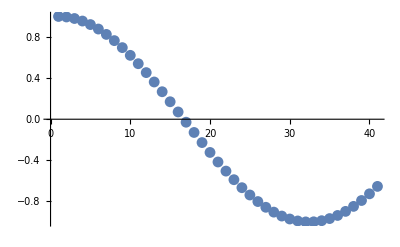

```mathematica
ListPlot[L]
```

```mathematica
Clear@x
```

```mathematica
line = Fit[L,{1, x, x^2, x^3,x^4,x^5}, x]
```

0.992611+0.0115418 x-0.00519196 x^2-0.0000146092 x^3+5.33627×10^-6 x^4-6.44406×10^-8 x^5

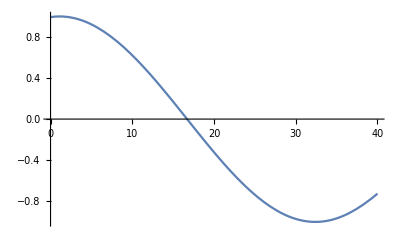

```mathematica
P1=Plot[line,{x,0,40}]
```

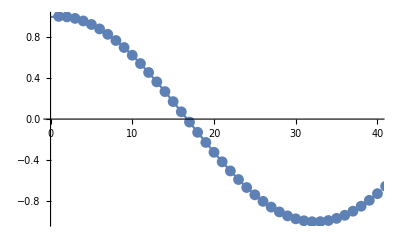

```mathematica
Show[Plot[line,{x,0,40}], ListPlot[L]]
```

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorListPlot::shdw: Symbol "ErrorListPlot" appears in multiple contexts {"ErrorBarPlots`", "Global`"}; definitions in context "ErrorBarPlots`" may shadow or be shadowed by other definitions.

```mathematica
L2=Table[{L[[i]], RandomReal[0.1]},{i, 1, 41}]
```

{{1.,0.0780182},{0.995004,0.0108338},{0.980067,0.0651489},{0.955336,0.0768386},{0.921061,0.0513905},{0.877583,0.0194099},{0.825336,0.0365667},{0.764842,0.0391219},{0.696707,0.0288901},{0.62161,0.00691915},{0.540302,0.0667998},{0.453596,0.00762789},{0.362358,0.0157088},{0.267499,0.0394734},{0.169967,0.0758955},{0.0707372,0.0698963},{-0.0291995,0.0471012},{-0.128844,0.0260375},{-0.227202,0.0674932},{-0.32329,0.0781895},{-0.416147,0.0789478},{-0.504846,0.078109},{-0.588501,0.0215534},{-0.666276,0.0958961},{-0.737394,0.0747763},{-0.801144,0.0462196},{-0.856889,0.0850578},{-0.904072,0.0369401},{-0.942222,0.0278825},{-0.970958,0.0633399},{-0.989992,0.0927225},{-0.999135,0.0492442},{-0.998295,0.00228367},{-0.98748,0.0190557},{-0.966798,0.0930316},{-0.936457,0.0564677},{-0.896758,0.0583411},{-0.8481,0.0602511},{-0.790968,0.0801752},{-0.725932,0.0653034},{-0.653644,0.0578955}}

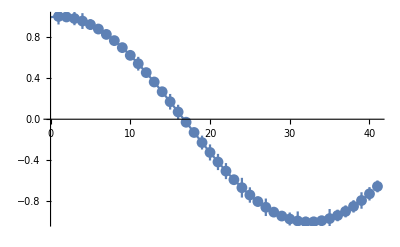

```mathematica
Show[ErrorListPlot[L2],P1]
```

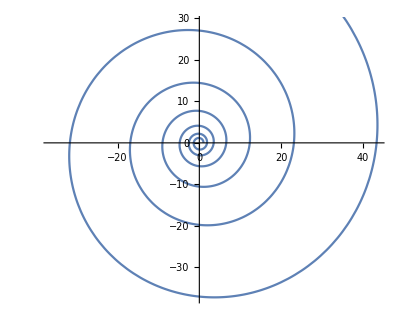

```mathematica
ParametricPlot[{Cos[t]*Exp[a*t],Sin[t]*Exp[a*t]},{t, 0, 40}]
```

```mathematica
Show[%74,PlotLabel->None,LabelStyle->{FontFamily->"Consolas",20,GrayLevel[0]}]
```

-Graphics-

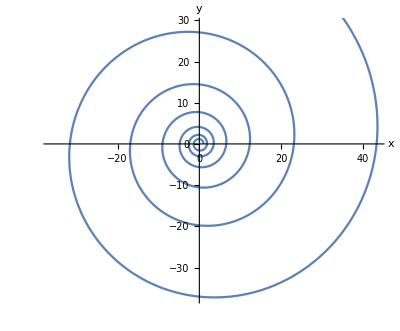

```mathematica
Show[%75,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Plot3D[Sin[Sqrt[x^2 + y^2]]/Sqrt[x^2 + y^2],{x, -10, 10},{y, -10, 10}, PlotRange->All]
```

-Graphics3D-

```mathematica
R1 = 1
```

1

```mathematica
ParametricPlot3D[{(R1 +a*Cos[phi])*Cos[psi],(R1 +a*Cos[phi])*Sin[psi],a*Sin[phi]},{psi, 0, 2*Pi}, {phi,  0, 2*Pi}]
```

-Graphics3D-

```mathematica
Plot[x^4+x^(-5),{x, 10^(-5), 10^5}](*Линейный*)
```

-Graphics-

```mathematica
LogLinearPlot[x^4+x^(-5),{x, 10^(-5), 10^5}](*x - логарифмический*)
```

-Graphics-

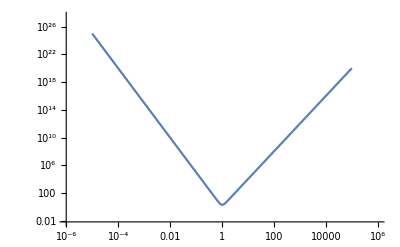

```mathematica
LogLogPlot[x^4+x^(-5),{x, 10^(-5), 10^5}](*x, y - логарифмические*)
```

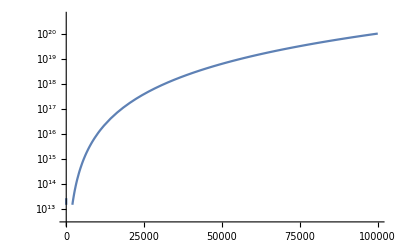

```mathematica
LogPlot[x^4+x^(-5),{x, 10^(-5), 10^5}](*y - логарифмический*)
```